## import

```mathematica
data=Association@Import[FileNameJoin[{NotebookDirectory[],"data.json"}]];
```

```mathematica
data
```

<|numberOfContainers→80,9,solutionsStat→{{236.523,236.523,233.577,233.577,233.577,232.983,232.983,231.987,231.987,230.959,230.959,129,210.266,210.266,210.266,209.871,209.871,209.871,209.871,209.871,209.871,209.871,209.871},3,{1}}|>
 |  |  |  |

```mathematica
isImport=True;
```

```mathematica
Clear[import]
import[input_,key_,isImport_]:=If[isImport,data[key],input]
```

## settings

### functions

```mathematica
getVarianteTwoArg=RandomVariate@MultinomialDistribution[#1,ConstantArray[1/#2,#2]]&;
```

### initial parameters

```mathematica
numberOfContainers=import[7,"numberOfContainers",isImport];
numberOfVehicles=import[2,"numberOfVehicles",isImport];
numberOfStacks=import[2,"numberOfStacks",isImport];
```

```mathematica
ϵ=0.1;
shareOfPairsBlocks=0.05;
```

## generate initial data

```mathematica
vertices1=Range@numberOfContainers;
vertices2=vertices1+numberOfContainers;
```

```mathematica
If[
isImport,
pointsVertices1=data["pointsVertices1"];pointsVertices2=data["pointsVertices2"],
{pointsVertices1,pointsVertices2}=Table[RandomReal[{1,5},{numberOfContainers,2}],2];
];
```

```mathematica
distanceMatrix=DistanceMatrix[pointsVertices1,pointsVertices2];
```

```mathematica
points=Join[pointsVertices1,pointsVertices2];
```

```mathematica
δ1=δ2=Ceiling@Mean@Flatten@distanceMatrix;
```

```mathematica
outArcs=MapThread[DirectedEdge,{vertices1,vertices2}];
inArcs=DeleteCases[Flatten[Outer[DirectedEdge,vertices2,vertices1]],i_->j_/;i-numberOfContainers==j];
startArcs=Thread[DirectedEdge[0,vertices1]];
endArcs=Thread[DirectedEdge[vertices2,2numberOfContainers+1]];
arcs=Join[startArcs,inArcs,outArcs,endArcs];
```

```mathematica
time=Join[
Association[#-> distanceMatrix⟦#⟦1⟧,#⟦2⟧-numberOfContainers⟧&/@outArcs],
Association[#-> distanceMatrix⟦#⟦2⟧,#⟦1⟧-numberOfContainers⟧&/@inArcs],
Association[#-> 0&/@startArcs],
Association[#-> 0&/@endArcs]
];
```

```mathematica
If[
isImport,
stacks=data["stacks"],
stacks=TakeList[RandomSample@vertices1,getVarianteTwoArg[numberOfContainers,numberOfStacks]]
];
```

```mathematica
If[
isImport,
pairsVertices1=data["pairsVertices1"];pairsVertices2=data["pairsVertices2"],
{pairsVertices1,pairsVertices2}=RandomSample[#,Floor[shareOfPairsBlocks Length@#]]&@Subsets[#,{2}]&/@{vertices1,vertices2};
];
```

```mathematica
relationsPairsVertices1=Flatten[Subsets[#,{2}]&/@stacks,1];
```

```mathematica
K=numberOfVehicles(Total[Max/@distanceMatrix]+Total[Max/@(distanceMatrixᵀ)]);
```

## 2Opt, 2HOpt, 4Opt functions

```mathematica
Clear[f]
f[x_]:=Total[distanceMatrix⟦#⟦1⟧,#⟦2⟧⟧&/@Partition[x,2,1]]+distanceMatrix⟦x⟦-1⟧,x⟦1⟧⟧
```

```mathematica
Clear[inverse]
inverse[permutation_,i1_,j1_]:=Module[
{p=permutation,sortedij=Sort[{i1,j1}],i,j,oldi},
i=sortedij⟦1⟧;
j=sortedij⟦2⟧;
If[
j-i==Length[p]-1,
oldi=p⟦i⟧;p⟦i⟧=p⟦j⟧;p⟦j⟧=oldi;p,
Join[p⟦1;;i-1⟧,Reverse[p⟦i;;j⟧],p⟦j+1;;Length@p⟧]
]
]
```

```mathematica
Clear[insert]
insert[permutation_,i_,j_]:=Module[
{p=permutation,element=permutation⟦j⟧},
p=Drop[p,{j}];Insert[p,element,i]
]
```

```mathematica
Clear[swap]
swap[permutation_,i_,j_]:=Module[
{p=permutation,element=permutation⟦i⟧},
p⟦i⟧=p⟦j⟧;p⟦j⟧=element;p
]
```

## curing routes

```mathematica
(*Пары для каждого маршрута, котрые надо проверить*)
Clear[pairsForRoute]
pairsForRoute[route_]:=Select[relationsPairsVertices1,MemberQ[route,#⟦1⟧]∧MemberQ[route,#⟦2⟧]&]
```

```mathematica
(*Устранение недопустимых решений*)
Clear[cureFunction]
cureFunction[routesOfTrip_]:=Module[
{routes=routesOfTrip,pairs,begin,pair,positions},
Do[
pairs=pairsForRoute[routes⟦i⟧];
Label[begin];
Do[
pair=pairs⟦j⟧;
positions=Flatten[Position[routes⟦i⟧,#]&/@pair];
If[
positions⟦1⟧<positions⟦2⟧,
routes⟦i⟧=swap[routes⟦i⟧,positions⟦1⟧,positions⟦2⟧];Goto[begin]
],
{j,Length[pairs]}
],
{i,Length[routes]}
];
routes
]
```

## find potentials

### variables

```mathematica
varsU=u/@Range[2numberOfContainers];
varsUOut=u[0,#]&/@Range[numberOfVehicles];
varsUIn=u[2numberOfContainers+1,#]&/@Range[numberOfVehicles];
```

```mathematica
varsYPV1=y@@@pairsVertices1;
varsYPV2=y@@@pairsVertices2;
```

```mathematica
vars=Join[varsU,varsUOut,varsUIn,varsYPV1,varsYPV2,{umax}];
```

### objfun

```mathematica
objfun={Total[varsUIn-varsUOut],umax}.{0.5,0.5};
```

```mathematica
c=Last@CoefficientArrays[objfun,vars];
```

### constraints

```mathematica
cons1=umax-varsUIn;
```

```mathematica
rhs1=ConstantArray[{0,1},Length[cons1]];
```

```mathematica
cons2=u[#⟦1⟧]-u[#⟦2⟧]&/@relationsPairsVertices1;
```

```mathematica
rhs2=ConstantArray[{δ1,1},Length[relationsPairsVertices1]];
```

```mathematica
cons31=u[#⟦2⟧]-u[#⟦1⟧]-K*y[#⟦1⟧,#⟦2⟧]&/@pairsVertices1;
```

```mathematica
rhs31=ConstantArray[{-δ2,-1},Length[pairsVertices1]];
```

```mathematica
cons32=u[#⟦1⟧]-u[#⟦2⟧]+K*y[#⟦1⟧,#⟦2⟧]&/@pairsVertices1;
```

```mathematica
rhs32=ConstantArray[{K-δ2,-1},Length[pairsVertices1]];
```

```mathematica
cons41=u[#⟦2⟧]-u[#⟦1⟧]-K*y[#⟦1⟧,#⟦2⟧]&/@pairsVertices2;
```

```mathematica
rhs41=ConstantArray[{-δ2,-1},Length[pairsVertices2]];
```

```mathematica
cons42=u[#⟦1⟧]-u[#⟦2⟧]+K*y[#⟦1⟧,#⟦2⟧]&/@pairsVertices2;
```

```mathematica
rhs42=ConstantArray[{K-δ2,-1},Length[pairsVertices2]];
```

```mathematica
lu=Join[
ConstantArray[{0,K},Length[varsU]+Length[varsUOut]+Length[varsUIn]],
ConstantArray[{0,1},Length[varsYPV1]+Length[varsYPV2]],
ConstantArray[{0,K},1]
];
```

```mathematica
domain=Join[
ConstantArray[Reals,Length[varsU]+Length[varsUOut]+Length[varsUIn]],
ConstantArray[Integers,Length[varsYPV1]+Length[varsYPV2]],
ConstantArray[Reals,1]
];
```

### gurobi settings

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"GurobiOptimization.wl"}]]
```

```mathematica
directory = "C:\\gurobi912\\win64\\bin\\";
```

### main function

```mathematica
(*Сокращенных маршруты преобразуются в полные*)
Clear[fullRoutes]
fullRoutes:=Table[Riffle[#⟦i⟧,#⟦i⟧+numberOfContainers],{i,Length[#]}]&
```

```mathematica
(*Дуги маршрутов полных маршрутов*)
Clear[pairsOfFullRoutes]
pairsOfFullRoutes[routes_]:=Flatten[Partition[#,2,1]&/@fullRoutes[routes],1]
```

```mathematica
Clear[findPotentials]
findPotentials[routes_]:=Module[{
cons5FullRoutes=fullRoutes[routes],
cons5Pairs=pairsOfFullRoutes[routes],
cons5,rhs5,cons6,rhs6,cons7,rhs7,m,b,
},
cons5=u[#⟦2⟧]-u[#⟦1⟧]&/@cons5Pairs;
rhs5={time[#⟦1⟧->#⟦2⟧],1}&/@cons5Pairs;
cons6=Flatten[Table[
If[Length[cons5FullRoutes⟦i⟧]==0,{},
{u[First[cons5FullRoutes⟦i⟧]]-u[0,i],u[2numberOfContainers+1,i]-u[Last[cons5FullRoutes⟦i⟧]]}
],{i,Length@cons5FullRoutes}]];
rhs6=ConstantArray[{0,1},Length[cons6]];
cons7=varsUOut;
rhs7={Length[#]*K,-1}&/@routes;
m=Last@CoefficientArrays[Join[cons1,cons2,cons31,cons32,cons41,cons42,cons5,cons6,cons7],vars];
b=Join[rhs1,rhs2,rhs31,rhs32,rhs41,rhs42,rhs5,rhs6,rhs7];
(*LinearProgramming[c,m,b,lu,domain]*)
GurobiOptimization[Normal@c,Normal@m,b,lu,domain,directory]
]
```

### target function

```mathematica
Clear[f]
f[routes_]:=Module[{
solution=Quiet@Check[findPotentials[routes],K],
umax,varsUIn,varsUOut
},
If[solution==K,Return[solution]];
umax=Last[solution];
varsUIn=solution⟦2numberOfContainers+numberOfVehicles+1;;2(numberOfContainers+numberOfVehicles)⟧;
varsUOut=solution⟦2numberOfContainers+1;;2numberOfContainers+numberOfVehicles⟧;
{Total[varsUIn-varsUOut],umax}.{0.5,0.5}
]
```

## simulated annealing

```mathematica
Clear[routesToAnnealing]
routesToAnnealing:=Flatten[Riffle[#,0]]&
```

```mathematica
Clear[routesFromAnnealing]
routesFromAnnealing[routes_]:=DeleteCases[#,0]&/@(Split[routes,#!=0&])
```

```mathematica
Clear[minimalPermut]
minimalPermut[routes_,i_,j_,mode_]:=Module[{p=RandomReal[],permutation=routesToAnnealing[routes]},
Switch[
mode,
1,MinimalBy[{#,f[#]}&/@(cureFunction[routesFromAnnealing[#]]&/@{inverse[permutation,i,j],insert[permutation,i,j],swap[permutation,i,j]}),Last]⟦1⟧,
2,MinimalBy[{#,f[#]}&/@(routesFromAnnealing[#]&/@{inverse[permutation,i,j],insert[permutation,i,j],swap[permutation,i,j]}),Last]⟦1⟧,
3,({#,f[#]}&/@{routesFromAnnealing@Which[p≤ 0.5,swap[permutation,i,j],p≤0.7,inverse[permutation,i,j],True,insert[permutation,i,j]]})⟦1⟧
]
]
```

### use cases minimalPermut

```mathematica
Clear[randomRoutes]
randomRoutes:=NestWhile[Flatten/@TakeList[Reverse/@stacks,getVarianteTwoArg[numberOfStacks,numberOfVehicles]]&,{{}},MemberQ[{}]]
```

```mathematica
initialRoutes=randomRoutes
```

{{24,62,69},{77,14,45,37,47,26,33,38,49,3,70,12,67,5,54,32,65,39,16,64,55,7,10,11,6,72,60,56,27,78},{75,57,58,18,34,71,41,19,53,48,66,8,29,80,25,42,4,59,21,28,52,43,40,73,22},{9,51,76,31,35},{68,36,15,2,74,61,17,30,23,79,1,50,46,20,44,13,63}}

```mathematica
random=RandomSample[Range[numberOfContainers+numberOfVehicles-1],2]
```

{3,43}

```mathematica
minimalPermut[initialRoutes,random⟦1⟧,random⟦2⟧,1]//AbsoluteTiming
```

{2.80838,{{{24,62,41,19,75,57,58,18,34,71},{56,27,78,16,64,55,7,10,11,6,72,60,32,65,39,67,5,54,38,49,3,70,12,77,14,45,37,47,26,33},{69,53,48,66,8,29,80,25,42,4,59,21,28,52,43,40,73,22},{9,51,76,31,35},{68,36,15,2,74,61,17,30,23,79,1,50,46,20,44,13,63}},236.829}}

```mathematica
minimalPermut[initialRoutes,random⟦1⟧,random⟦2⟧,2]//AbsoluteTiming
```

{2.12893,{{{24,62,19},{77,14,45,37,47,26,33,38,49,3,70,12,67,5,54,32,65,39,16,64,55,7,10,11,6,72,60,56,27,78},{75,57,58,18,34,71,41,69,53,48,66,8,29,80,25,42,4,59,21,28,52,43,40,73,22},{9,51,76,31,35},{68,36,15,2,74,61,17,30,23,79,1,50,46,20,44,13,63}},237.929}}

```mathematica
minimalPermut[initialRoutes,random⟦1⟧,random⟦2⟧,3]//AbsoluteTiming
```

{0.993071,{{{24,62,19,69},{77,14,45,37,47,26,33,38,49,3,70,12,67,5,54,32,65,39,16,64,55,7,10,11,6,72,60,56,27,78},{75,57,58,18,34,71,41,53,48,66,8,29,80,25,42,4,59,21,28,52,43,40,73,22},{9,51,76,31,35},{68,36,15,2,74,61,17,30,23,79,1,50,46,20,44,13,63}},238.658}}

### simulated annealing function

```mathematica
Clear[simulatedAnnealing]
simulatedAnnealing[routes_,maxIteration_,initialTemperature_,endTemperature_,a_,mode_]:=Module[
{currentRoutes=routes,t=initialTemperature,randomChoice,p,currentf,fy,history={},candidate,
listToChoose=Range[numberOfContainers+numberOfVehicles-1]},
AppendTo[history,{currentRoutes,f[currentRoutes]}];
Do[
randomChoice=RandomSample[listToChoose,2];
candidate=minimalPermut[currentRoutes,randomChoice⟦1⟧,randomChoice⟦2⟧,mode];
fy=candidate⟦2⟧;
currentf=f[currentRoutes];
If[
fy≤ currentf,
currentRoutes=candidate⟦1⟧,
p=Exp[(-(fy-currentf))/t];If[RandomReal[]≤ p,currentRoutes=candidate⟦1⟧]
];
AppendTo[history,{currentRoutes,currentf}];
t=t*a;
If[t<=endTemperature,Break[]],
{i,maxIteration}];
history
]
```

## main

### results

```mathematica
initialRoutes=import[randomRoutes,"initialRoutes",isImport]
```

{{24,62,69,77,14,45,37,47,26,33,38,49,3,70,12,67,5,54,32,65,39},{16,64,55,7,10,11,6,72,60,56,27,78,75,57,58,18,34,71,41,19,53,48,66,8,29,80},{25,42,4,59,21,28,52,43,40,73,22},{9,51,76,31,35,68,36,15,2,74,61,17,30,23},{79,1,50,46,20,44,13,63}}

```mathematica
f[initialRoutes]
```

231.737

```mathematica
solution=If[isImport,data["solution"],simulatedAnnealing[initialRoutes,800,0.025,10^-10,0.99,1]];
```

```mathematica
finalRoute=solution⟦-1,1⟧
```

{{40,38,77,14,45,79,1,15,19,50,46,2,74,61,17,32,71,9,23,51,76,31,35},{43,24,73,22,25,62,42,4,37,20,44,13,49,47,59,3,70,5,30,12,65,69,8,36,39},{16,64,75,57,55,41,7,10,58,11,56,6,18,34,63,67},{27,78,72,54,60,26,48,33,66,29,80},{21,28,52,53,68}}

```mathematica
finalRoutef=solution⟦-1,2⟧
```

193.948

### target function value

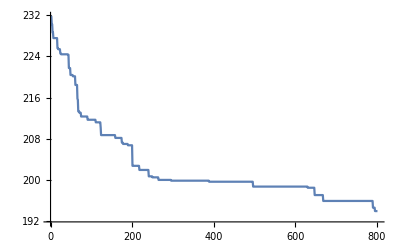

```mathematica
ListLinePlot[solution⟦All,2⟧]
```

```mathematica
Clear[listLinePlot]
listLinePlot[fullSolution_,step_,n_]:=ListLinePlot[
points⟦#⟧&/@If[n≠numberOfVehicles+1,fullSolution⟦step,1,n⟧,fullSolution⟦step,1⟧],
PlotRange->{{1,5},{1,5}},
PlotLegends->If[n≠numberOfVehicles+1,StringJoin[ToString[n]," vehicle"],(StringJoin[ToString[#]," vehicle"]&/@Range[numberOfVehicles])],
Epilog->PointSize[Large],ImageSize->500,Mesh->All
]
```

```mathematica
Clear[graph]
graph[fullSolution_,step_,n_]:=Module[{edgesPairs,edgesStyle,
c=Table[Hue[i/numberOfVehicles,1,1],{i,numberOfVehicles}]},
If[
n≠numberOfVehicles+1,
edgesPairs=DirectedEdge@@@Partition[fullSolution⟦step,1,n⟧,2,1],
edgesPairs=DirectedEdge@@@Partition[#,2,1]&/@fullSolution⟦step,1⟧
];
If[
n≠numberOfVehicles+1,
edgesStyle=Flatten[Table[edgesPairs⟦j⟧->c⟦n⟧,{j,Length[edgesPairs]}]];,
edgesStyle=Flatten[Table[edgesPairs⟦i,j⟧->c⟦i⟧,{i,numberOfVehicles},{j,Length[edgesPairs⟦i⟧]}]]
];
Graph[Flatten@edgesPairs,EdgeStyle->edgesStyle,VertexLabels->"Name",VertexCoordinates->Table[i-> points⟦i⟧,{i,1,Length[points]}],ImageSize->500]
]
```

```mathematica
Clear[manipulate]
manipulate[solution_,plot_]:=Module[{fullSolution},
fullSolution={fullRoutes[#⟦1⟧],#⟦2⟧}&/@solution;
Manipulate[Column[{
Text[Style["Target function = "<>ToString[solution⟦step,2⟧],24]],
Text[Style[StringJoin[MapIndexed["Vehicle "<>ToString[#2⟦1⟧]<>" has "<>ToString[Length[#1]]<>" points. "&,fullSolution⟦step,1⟧]],14]],
Switch[image,1,listLinePlot[fullSolution,step,vehicle],2,graph[fullSolution,step,vehicle]]
}],{step,1,Length[solution],1},{image,{1->"List Line Plot",2->"Graph"}},{vehicle,Join[{numberOfVehicles+1-> "all"},Table[m-> (ToString[m]<>" vehicle"),{m,1,numberOfVehicles}]]}]
]
```

```mathematica
manipulate[solution,listLinePlot]
```

### map vizualization

```mathematica
newPoints={#⟦1⟧+54,#⟦2⟧+33}&/@points;
```

```mathematica
GeoListPlot[Map[GeoPosition[newPoints⟦#⟧]&,fullRoutes[finalRoute]],Joined->True]
```

-Graphics-

### statistics

```mathematica
Clear[statistic]
statistic[n_,iteration_,mode_]:=Quiet@Module[{initialRoutes=randomRoutes,solutions={},solution},
Do[solution=simulatedAnnealing[initialRoutes,iteration,0.55,10^-10,0.99,mode];
AppendTo[solutions,solution⟦All,2⟧],
{i,n}];
solutions]
```

```mathematica
solutionsStat=If[isImport,data["solutionsStat"],statistic[5,150,1]];
```

```mathematica
Clear[plotStatistic]
plotStatistic[solutions_]:=Quiet@Module[{initialRoutes=randomRoutes,values={},graphics={},solution,stat,colors,str,n=Length@solutions},
Do[
AppendTo[values,Last@solution];
AppendTo[graphics,ListLinePlot[solution,PlotTheme->"Business"]],
{solution,solutions}];
stat={Max[values],Mean[values],Min[values]};
colors=Permutations[{Magenta,LightGray,LightGray}];
str=StringJoin[ToString[#]," вариант"]&/@Range[n];
If[n>2,
values=Join[values,stat];
graphics=Join[graphics,ListLinePlot[ConstantArray[#,n]&/@stat,PlotTheme->"Business",PlotStyle->#]&/@colors];
str=Join[str,{"Худший", "Средний","Лучший"}];
];
Grid[Transpose@{str,values,graphics},Frame->All]
]
```

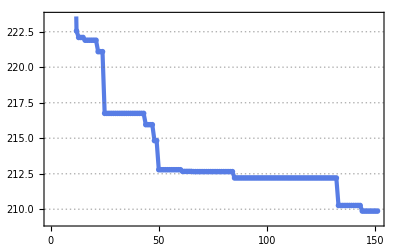
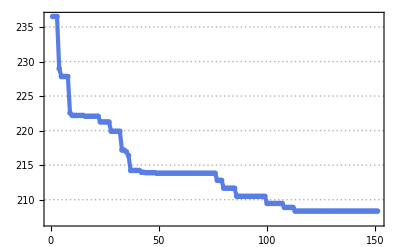
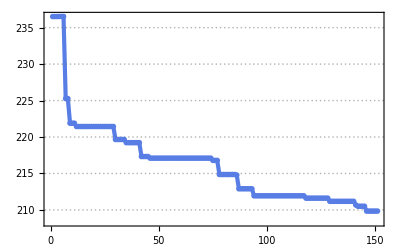
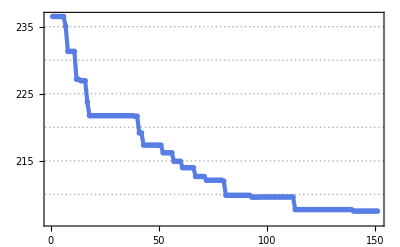
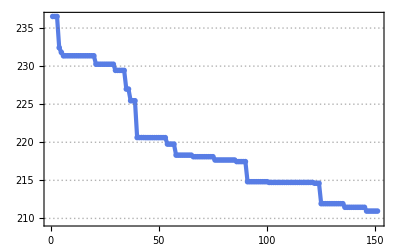
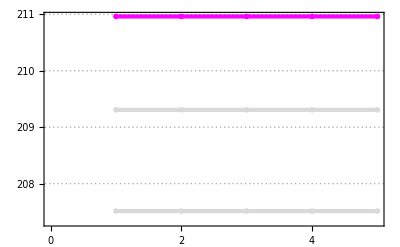
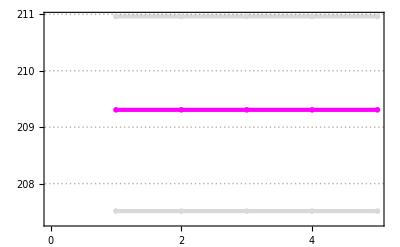
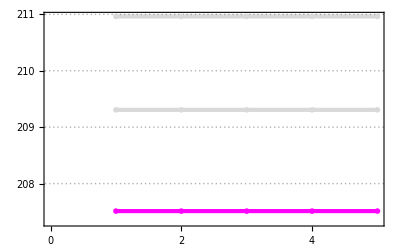
1 вариант | 209.871 | -Graphics-
2 вариант | 208.348 | -Graphics-
3 вариант | 209.841 | -Graphics-
4 вариант | 207.512 | -Graphics-
5 вариант | 210.963 | -Graphics-
Худший | 210.963 | -Graphics-
Средний | 209.307 | -Graphics-
Лучший | 207.512 | -Graphics-

```mathematica
plotStatistic[solutionsStat]
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"data.json"}],{
"numberOfContainers"->numberOfContainers,
"numberOfVehicles"->numberOfVehicles,
"numberOfStacks"->numberOfStacks,
"pointsVertices1"->pointsVertices1,
"pointsVertices2"->pointsVertices2,
"stacks"->stacks,
"pairsVertices1"->pairsVertices1,
"pairsVertices2"->pairsVertices2,
"initialRoutes"->initialRoutes,
"solution"->solution,
"solutionsStat"-> solutionsStat
}];*)
```